```mathematica
<<PlotLegends`
```

```mathematica
Calculation of Scattering Rates Γeff(n)
```

```mathematica
tab = Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[4 10^-5  ]] == Re[fun[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la]];
{n,lam},{n,0,10}]
```

Set::write: Tag Times in 1\ 485760. is Protected.

Set::write: Tag Times in 0\ 485760. is Protected.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in 0\ 485760. is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{0,0},{1,25921.7},{2,51573.3},{3,76924.2},{4,102178.},{5,127517.},{6,153126.},{7,179203.},{8,205971.},{9,233639.},{10,262521.}}

```mathematica
If[n == 0, lam=0, dummy = 0];
```

```mathematica
If[n == 0, α=1, dummy = 0]
```

```mathematica
n
```

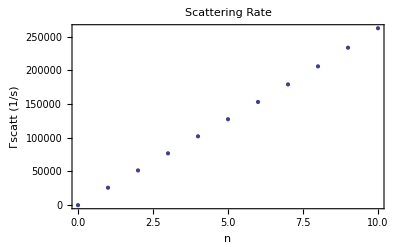

```mathematica
ListPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True]
```

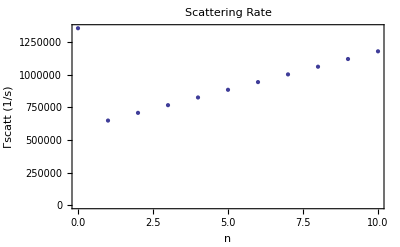

```mathematica
ListPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True]
```

```mathematica
Scattering Rate As a Function of Raman and Repump Coupling strengths.
```

```mathematica
tabrepump =Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
Ω1 = 50 2 Pi 10^3;
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
(*ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];*)
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[4 10^-5  ]] == Re[fun[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la]];
{ΩR,lam},{ΩR,0,4 10^6, 2 10^4}],{n,1,10}];
```

Set::write: Tag Times in 0\ 485760. is Protected.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.0538473.

Set::write: Tag Times in 0\ 485760. is Protected.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.0329955.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Set::write: Tag Times in 0\ 485760. is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.0516823.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{{0,{}⟦1,2⟧},{20000,116631.65476168178},{40000,113257.50972370322},{60000,108385.53409544435},{80000,102687.11907788413},{100000,96722.55756227943},{120000,90846.59080458581},{140000,85263.84553766997},{160000,80075.42705264219},{180000,75319.92575040026},{200000,71006.60486477116},{220000,67124.04947523099},{240000,63653.48332128069},{260000,60572.20235600176},{280000,57857.11512418764},{300000,55485.2811646457},{320000,53435.00893428954},{340000,51685.77532857563},{360000,50218.44563567729},{380000,49014.97049284383},{400000,48058.43673447862},{420000,47332.593552172904},{440000,46822.03195537333},{460000,46511.751534408475},{480000,46387.0389834822},{500000,46433.43299836118},{520000,46636.53237861939},{540000,46981.896024383655},{560000,47454.91554912172},{580000,48040.77813857017},{600000,48724.47653484474},{620000,49490.69690443282},{640000,50323.8754572983},{660000,51208.190362147274},{680000,52127.65661237542},{700000,53066.26569507669},{720000,54007.99089558368},{740000,54937.105930779086},{760000,55838.27671231324},{780000,56696.81829546512},{800000,57498.929876302005},{820000,58231.949590457414},{840000,58884.51074133497},{860000,59446.91954609394},{880000,59911.1549679287},{900000,60271.081988398975},{920000,60522.492164171235},{940000,60663.17271968333},{960000,60692.745288633574},{980000,60612.611449463286},{1000000,60425.728859771356},{1020000,60136.480083732975},{1040000,59750.37213535922},{1060000,59273.833164119744},{1080000,58713.93969725255},{1100000,58078.21281068223},{1120000,57374.40663813592},{1140000,56610.34137531338},{1160000,55793.73986428335},{1180000,54932.09895652764},{1200000,54032.630850630056},{1220000,53102.18543621404},{1240000,52147.17588986889},{1260000,51173.59502790476},{1280000,50186.986461161716},{1300000,49192.40451033076},{1320000,48194.52400613143},{1340000,47197.51561162469},{1360000,46205.19936884456},{1380000,45220.947029966155},{1400000,44247.78737767051},{1420000,43288.398930106516},{1440000,42345.06486584224},{1460000,41419.83388355487},{1480000,40514.41510473446},{1500000,39630.268227443725},{1520000,38768.54324720475},{1540000,37930.17544239083},{1560000,37115.86552682121},{1580000,36326.06850736447},{1600000,35561.100079075375},{1620000,34821.026682318734},{1640000,34105.76627707988},{1660000,33415.06819245657},{1680000,32748.538173472527},{1700000,32105.654467310764},{1720000,31485.766846933817},{1740000,30888.11647472933},{1760000,30311.864219956016},{1780000,29756.09565879467},{1800000,29219.823523167368},{1820000,28702.006283219634},{1840000,28201.580923815192},{1860000,27717.428383833318},{1880000,27248.462717778253},{1900000,26793.562425551532},{1920000,26351.61469338837},{1940000,25921.56014365098},{1960000,25502.319564350128},{1980000,25092.89213159348},{2000000,24692.291067448892},{2020000,24299.61591771584},{2040000,23913.98738470086},{2060000,23534.621155934277},{2080000,23160.774317720243},{2100000,22791.802647250533},{2120000,22427.110379044203},{2140000,22066.191840573763},{2160000,21708.609885568578},{2180000,21354.01403381999},{2200000,21002.128578645803},{2220000,20652.749224683528},{2240000,20305.732291912045},{2260000,19961.061441213435},{2280000,19618.714822936796},{2300000,19278.787312030618},{2320000,18941.4049108643},{2340000,18606.784579944357},{2360000,18275.163339279457},{2380000,17946.837281475026},{2400000,17622.16029706333},{2420000,17301.480575992126},{2440000,16985.21978131987},{2460000,16673.789576424646},{2480000,16367.617855069255},{2500000,16067.175681003411},{2520000,15772.867668497209},{2540000,15485.15692928094},{2560000,15204.500408489917},{2580000,14931.242727479193},{2600000,14665.774371385387},{2620000,14408.461203122937},{2640000,14159.568606991586},{2660000,13919.39922777577},{2680000,13688.160340257555},{2700000,13466.004536354769},{2720000,13253.02218977053},{2740000,13049.283833554115},{2760000,12854.761149673599},{2780000,12669.426070590938},{2800000,12493.096361297834},{2820000,12325.593087364194},{2840000,12166.684273835323},{2860000,12016.052253622729},{2880000,11873.355292494402},{2900000,11738.15233169041},{2920000,11610.064609135332},{2940000,11488.52944704438},{2960000,11373.052728182167},{2980000,11263.10802679002},{3000000,11158.088995173732},{3020000,11057.414280017083},{3040000,10960.491292215727},{3060000,10866.7140361393},{3080000,10775.46627972501},{3100000,10686.186105805322},{3120000,10598.225339917259},{3140000,10511.148352008546},{3160000,10424.310673035152},{3180000,10337.206524723859},{3200000,10249.437274093769},{3220000,10160.500804908324},{3240000,10070.002572711126},{3260000,9977.660197101484},{3280000,9883.078001720023},{3300000,9786.10933268284},{3320000,9686.464897738619},{3340000,9584.018786295072},{3360000,9478.670876044976},{3380000,9370.403805674736},{3400000,9259.199111040158},{3420000,9145.123821929887},{3440000,9028.281349796312},{3460000,8908.835170274342},{3480000,8787.005682912995},{3500000,8663.039298302252},{3520000,8537.20282254465},{3540000,8409.851325506435},{3560000,8281.323974643636},{3580000,8152.025340304018},{3600000,8022.361786026871},{3620000,7892.778135758094},{3640000,7763.709506257989},{3660000,7635.6425502172915},{3680000,7509.020428937941},{3700000,7384.306021446195},{3720000,7262.003165872333},{3740000,7142.50806765501},{3760000,7026.242411179468},{3780000,6913.665455828121},{3800000,6805.134856330003},{3820000,6700.984140233189},{3840000,6601.583244273499},{3860000,6507.143199839801},{3880000,6417.909785238351},{3900000,6334.131234594944},{3920000,6255.860670099458},{3940000,6183.196437999698},{3960000,6116.234253472025},{3980000,6054.914981961151},{4000000,5999.147317259636}}}
```

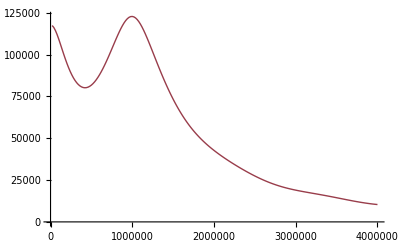
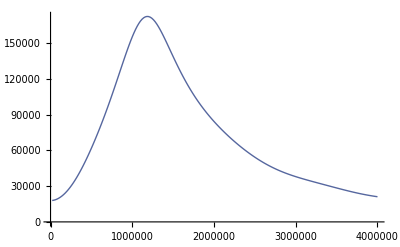
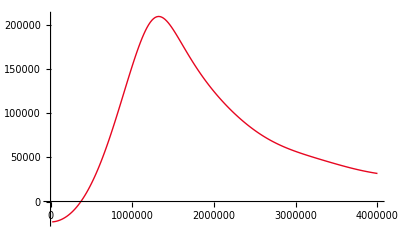
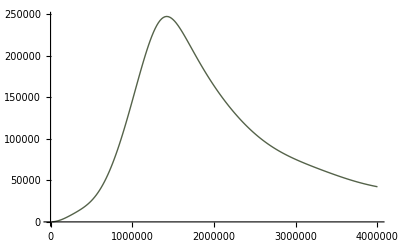
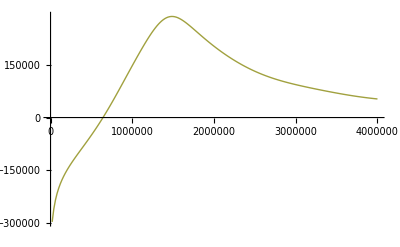
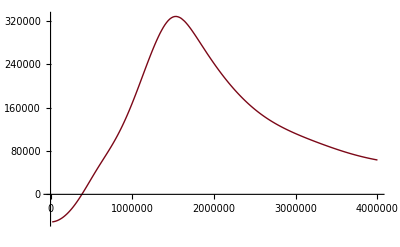
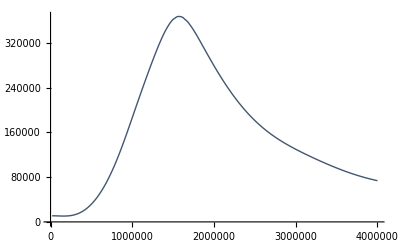
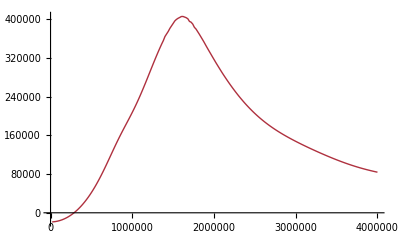

```mathematica
repumplots = Table[ListLinePlot[tabrepump[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

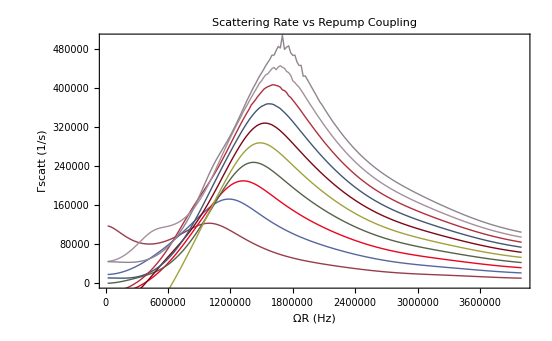

```mathematica
Show[repumplots , PlotRange -> {All,{0,500000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```

```mathematica
tabraman=Table[ Table[
(*alpha factor to be guessed /measured*)
α = 0.6;
Γ = 1.84 10^6;
Ωfree = 2 Pi 30.6 10^3;
δ1 = 1;
δ2 = 1;
η = 0.2;
(*Ω1 = 50 2 Pi 10^3;*)
Ωn = Ω1 Sqrt[n];(*(√((n!)/((n+n-1-n)!))(ⅈ η 1)^(n-1-n)LaguerreL[n,n-1-n,(η 1)^2]*Exp[-η^2/2])^2;*)
hbar = 1.0545718×10^-34;
λ = 455.527 10^-9 ;
Int = 0.9 10^-3/(10^-4);
h = 2 Pi *hbar;
c = 2.997 10^8;
ΩR = Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)];
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0]
Γ1 = α η^2 (n+1) Γ;
Γ2 = (1-α)(1-η^2(2n - 1))Γ;
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10*10^-1}, MaxSteps-> 100000];
fun=ρ33/.First[sol];
expsol = Solve[Re[fun[4 10^-5  ]] == Re[fun[1 10^-5 ]] Exp[-l 3 10^-5 ],l];
la = l /. expsol;
If[n==0, lam = 0, lam = First[la]];
{Ω1,lam},{Ω1,0,2.5 10^6, 2 10^4}],{n,1,10}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00730591.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00719219.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 0.00706502.

General::stop: Further output of NDSolve :: mxst will be suppressed during this calculation.

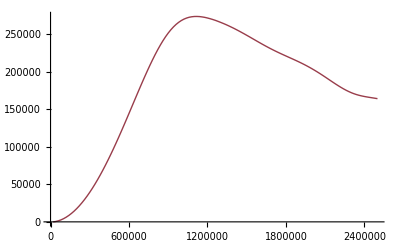
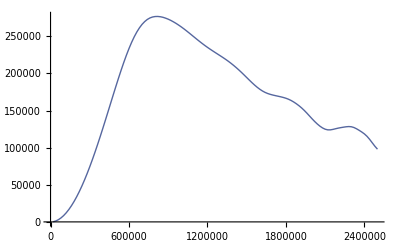
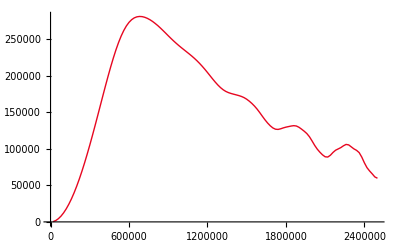
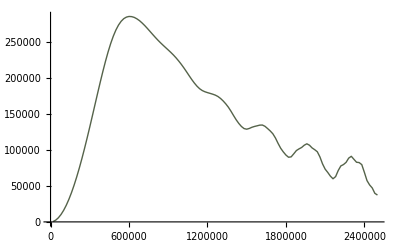
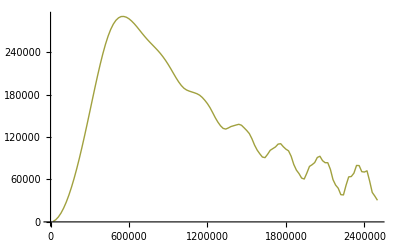
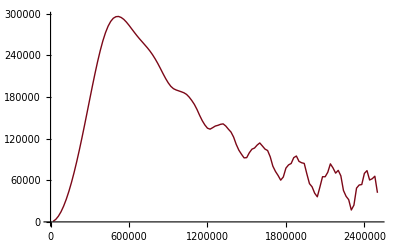
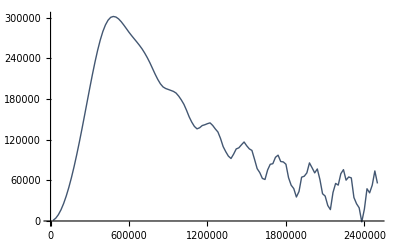
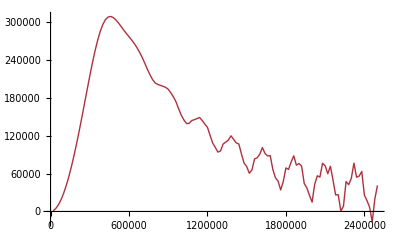

```mathematica
ramanplots = Table[ListLinePlot[tabraman[[n]], PlotStyle-> ColorData[n,"ColorList"]],{n,1,10}]
```

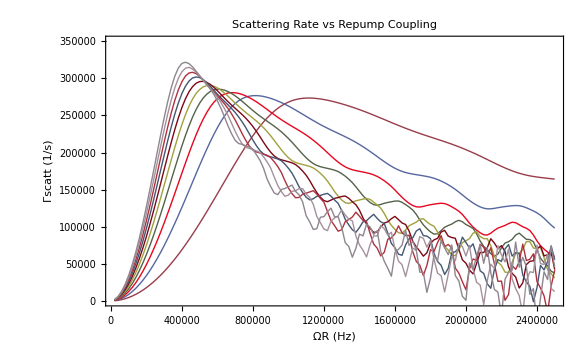

```mathematica
Show[ramanplots , PlotRange -> {All,{0,350000}}, FrameLabel-> {"ΩR (Hz)","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate vs Repump Coupling", Frame-> True]
```